1

функция Начальная

(3 (1-√(x^2+y^2)))/π

-Graphics3D-

Функция частичного распеределения x

(3 (√(1-x^2)-x^2 Log[(1+√(1-x^2))/Abs[x]]))/π

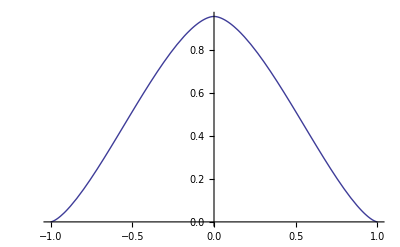

(3 (√(1-x^2)-x^2 Log[(1+√(1-x^2))/Abs[x]]))/π[0.4]

1

функция условного расделения

(1-√(x^2+y^2))/(√(1-x^2)-x^2 Log[(1+√(1-x^2))/Abs[x]])

Plot::exclul: {Im[x^2 + y^2] - 0, -Im[x^2] - 0, -Im[x^2] - 0, Im[1 + √1 + Times[« 2 »]/Abs[x]] - 0} must be a list of equalities or real-valued functions.

-Graphics-

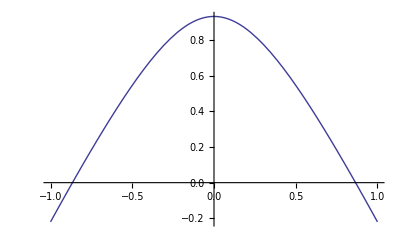

(π (0.572958+0.190986 √(0.16+x^2)-0.477465 √(1.+x^2)+0.477465 x^2 Log[0.4+√(0.16+x^2)]-0.477465 x^2 Log[1.+√(1.+x^2)]))/(3 (√(1-x^2)-x^2 Log[(1+√(1-x^2))/Abs[x]]))

(3 y-3/2 y √(x^2+y^2)-3/2 x^2 Log[y+√(x^2+y^2)])/π

```mathematica
R=1
Начальная функция
f=3/π(R-Sqrt[x^2+y^2])

Plot3D[f,{x,-R,R},{y,-R,R}]
 Функция частичного распеределения x
g=3/π*(Sqrt[1-x^2]-(x^2) *Log[(Sqrt[1-x^2]+1)/Abs[x]]) 
Plot[g,{x,-R,R}]
g[0.4]
Integrate[g,{x,-1,1}]
функция условного расделения
k=f/g
Plot[k,{x,-R,R}]
Plot[1.86294 (1-Sqrt[0.25+x^2]),{x,-R,R}]
p=(Integrate[f,{y,0.4,1}])/g
Integrate[f,y]
```